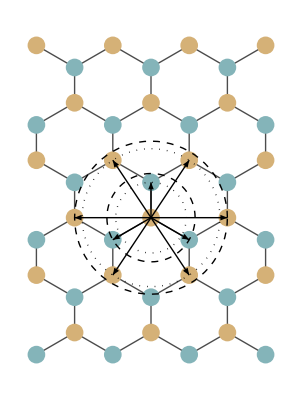

```mathematica
Clear[a,δa1,δa2,L1,L2,dom,a1,a2,a3,as,bs,uc,t1,t2,tnnn,ts,tnnns,tnnnpr]
a=1;
{δa1,δa2}={0.0,0.0};
{δa1,δa2}={0,0.2};
{δa1,δa2}={0.2,0.0};
{dtda1,dtda2}=-3/3*{1,1};
{L1,L2} = 12{1,1}+{1,0};
dom={4.2,4.5};

a1:= {0,a-δa1};
a2:= {√3/2(a-δa2),-a/2};
a3:={-√3/2(a-δa2),-a/2};
as:={a1,a2,a3};
bs:={a2-a3,a3-a1,a1-a2,a1-a3,a2-a1,a3-a2};
uc :={0,a2};

styles = {Dashed,Dotted};
nas=Sort[DeleteDuplicates[Norm[#]&/@as],Greater];
nbs=Sort[DeleteDuplicates[Norm[#]&/@bs],Greater];
styles = styles[[;;Length[nas]]];

latt=Flatten[Table[{n1*bs[[2]]+n2*bs[[3]]+uc[[i]],i},{n1,L1},{n2,L2},{i,2}],2];

orig=IntegerPart[L2/2]*bs[[3]]+IntegerPart[L1/2]bs[[2]];
domain=Rectangle[orig-dom+{1.4,1},orig+dom+{-1,-0.5}];
test=RegionMember[domain,#[[1]]]&/@latt;
latt=Pick[latt,test];

c1={213,177,119}/255;c2={132,180,185}/255;
color={RGBColor[Sequence@@c1],RGBColor[Sequence@@c2]};

graph=NearestNeighborGraph[latt[[All,1]],{All,1.01a},EdgeStyle->Black];
lattice=Graphics[{color[[#[[2]]]],Disk[#[[1]],0.2]}&/@latt];
nnVecs=Graphics[{{#[[2]],Circle[orig,#[[1]]]}&/@({nas,styles}ᵀ),Arrow[{orig,orig+#}]&/@as}];
nnnVecs=Graphics[{{#[[2]],Circle[orig,#[[1]]]}&/@({nbs,styles}ᵀ),Arrow[{orig,orig+#}]&/@bs}];
plot=Show[graph,lattice,nnVecs,nnnVecs]
```

```mathematica
Clear[a,δa1,δa2]
```

```mathematica
δa1=δa;
δa2=0;
```

```mathematica
as
bs
```

{{0,a-δa},{(√3 a)/2,-a/2},{-(√3 a)/2,-a/2}}

{{√3 a,0},{-(√3 a)/2,-(3 a)/2+δa},{-(√3 a)/2,(3 a)/2-δa},{(√3 a)/2,(3 a)/2-δa},{(√3 a)/2,-(3 a)/2+δa},{-√3 a,0}}

```mathematica
(*SetDirectory[NotebookDirectory[]<>"../CORE/figures/"]
Export["quinoid2.pdf",plot]*)
```

```mathematica
Clear[h1]
h1[kx_,ky_]:=ComplexExpand[FullSimplify[TrigExpand[ComplexExpand[-Sum[v[[2]] ⅇ^(ⅈ {kx,ky}.v[[1]]),{v,{as,{t1[1],t1[2],t1[2]}}ᵀ}]]]]]
h1[kx,ky]//FullSimplify
Solve[(h1[kx,ky]/.{ky->0})==0,kx]
```

-ⅇ^(ⅈ ky (a-δa)) t1[1]-2 ⅇ^(-1/2 ⅈ a ky) Cos[1/2 √3 a kx] t1[2]

{{kx→ConditionalExpression[(2 (-ArcCos[-t1[1]/(2 t1[2])]+2 π C[1]))/(√3 a), C[1]∈ℤ]},{kx→ConditionalExpression[(2 (ArcCos[-t1[1]/(2 t1[2])]+2 π C[1]))/(√3 a), C[1]∈ℤ]}}

```mathematica
Clear[h2]
h2[kx_,ky_]:=ComplexExpand[FullSimplify[TrigExpand[ComplexExpand[-Sum[v[[2]] ⅇ^(ⅈ {kx,ky}.v[[1]]),{v,{bs,{t2[1],t2[2],t2[2],t2[2],t2[2],t2[1]}}ᵀ}]]]]]
h2[kx,ky]//FullSimplify
```

-2 (Cos[√3 a kx] t2[1]+2 Cos[1/2 √3 a kx] Cos[(3 a ky)/2-ky δa] t2[2])

```mathematica
Clear[H]
H[kx_,ky_]:={{h2[kx,ky],ComplexExpand[h1[kx,ky]*]},{h1[kx,ky],h2[kx,ky]}}
```

```mathematica
1/2 Tr[H[kx,ky].PauliMatrix[1]]//Simplify//MatrixForm
```

-Cos[ky (a-δa)] t1[1]-2 Cos[1/2 √3 a kx] Cos[(a ky)/2] t1[2]

```mathematica
Clear[d]
d[kx_,ky_]:={h2[kx,ky],-Cos[ky (a-δa)] t1[1]-2 Cos[1/2 √3 a kx] Cos[(a ky)/2] t1[2],-Sin[ky (a-δa)] t1[1]+2 Cos[1/2 √3 a kx] Sin[(a ky)/2] t1[2]}
```

```mathematica
d[kx,ky].Table[PauliMatrix[i],{i,0,2}]-H[kx,ky]//Simplify
```

{{0,0},{0,0}}

```mathematica
Norm[d[kx,ky][[2;;]]]//ComplexExpand//FullSimplify
Clear[Epm]
Epm[kx_,ky_]:=√(t1[1]^2+4 Cos[1/2 √3 a kx] Cos[(3 a ky)/2-ky δa] t1[1] t1[2]+2 (1+Cos[√3 a kx]) t1[2]^2)
```

√(t1[1]^2+4 Cos[1/2 √3 a kx] Cos[(3 a ky)/2-ky δa] t1[1] t1[2]+2 (1+Cos[√3 a kx]) t1[2]^2)

```mathematica
s1=Join[{Normal[kx->+(2 ArcCos[-t1[1]/(2 t1[2])])/(√3 a)],ky->0}]
s2=Join[{Normal[kx->-(2 ArcCos[-t1[1]/(2 t1[2])])/(√3 a)],ky->0}]
```

{kx→(2 ArcCos[-t1[1]/(2 t1[2])])/(√3 a),ky→0}

{kx→-(2 ArcCos[-t1[1]/(2 t1[2])])/(√3 a),ky→0}

```mathematica
d[kx,ky]/.s1
d[kx,ky]/.s2
```

{-2 Cos[2 ArcCos[-t1[1]/(2 t1[2])]] t2[1]+(2 t1[1] t2[2])/t1[2],0,0}

{-2 Cos[2 ArcCos[-t1[1]/(2 t1[2])]] t2[1]+(2 t1[1] t2[2])/t1[2],0,0}

```mathematica
(Grad[#,{kx,ky}]&/@d[kx,ky])/.s1//FullSimplify
(Grad[#,{kx,ky}]&/@d[kx,ky])/.s2//FullSimplify
%+%%//FullSimplify
```

{{(a √(12-(3 t1[1]^2)/t1[2]^2) (-t1[1] t2[1]+t1[2] t2[2]))/t1[2],0},{1/2 a √(12-(3 t1[1]^2)/t1[2]^2) t1[2],0},{0,-3/2 a t1[1]+δa t1[1]}}

{{(a √(12-(3 t1[1]^2)/t1[2]^2) (t1[1] t2[1]-t1[2] t2[2]))/t1[2],0},{-1/2 a √(12-(3 t1[1]^2)/t1[2]^2) t1[2],0},{0,-3/2 a t1[1]+δa t1[1]}}

{{0,0},{0,0},{0,(-3 a+2 δa) t1[1]}}

```mathematica
ux=(a √(12-(3 t1[1]^2)/t1[2]^2) (-t1[1] t2[1]+t1[2] t2[2]))/t1[2];
uy=0;
vx=1/2 a √(12-(3 t1[1]^2)/t1[2]^2) t1[2];
vy=-3/2 a t1[1]+δa t1[1];
```

```mathematica
E0=(h2[kx,ky]/.s1);
```

```mathematica
Clear[Hlin,Elin]
Hlin[kx_,ky_]:=ux*kx*PauliMatrix[0]+(χ vx*PauliMatrix[1]*kx+vy*PauliMatrix[2]*ky);
Elin[kx_,ky_]=E0+(Eigenvalues[Hlin[kx,ky]])//FullSimplify;
```

```mathematica
χ=-1
Manipulate[Plot3D[Evaluate@(Elin[kx,ky]/.{t1[1]->t11,t1[2]->t12,t2[1]->t21,t2[2]->t22,δa->da,a->1}),{kx,-π,π},{ky,-π,π},AxesLabel->{"kx","ky","Epm"},ViewPoint->Front],{{da,0},-1,1},{{t11,1},0,2},{{t12,1},0,2},{{t21,1},0,2},{{t22,0},0,2}]
```

-1

```mathematica
Manipulate[plot=Show[Plot3D[Evaluate@(h2[kx,ky]+Epm[kx,ky]{+1,-1}/.{t1[1]->t11,t1[2]->t12,t2[1]->t21,t2[2]->t22,δa->da,a->1}),{kx,0.2π,2.1π},{ky,-0.3π,1.7π},PlotTheme->"Scientific",PlotPoints->100,Boxed->False,Axes->False,BoxRatios->{1,1,1},ViewPoint->{0.5,-2,0.5}]
,
Graphics3D[{Opacity[0.5],Lighter[Red,0.6],Sphere[({kx,ky,E0}/.s1)/.{t1[1]->t11,t1[2]->t12,t2[1]->t21,t2[2]->t22,δa->da,a->1},0.7]}]
,
Graphics3D[{Opacity[0.5],Lighter[Green,0.6],Sphere[({kx+7.25,ky,E0}/.s2)/.{t1[1]->t11,t1[2]->t12,t2[1]->t21,t2[2]->t22,δa->da,a->1},0.7]}]
(*,
Plot3D[Evaluate@(Elin[kx-s1[[1,2]],ky]/.{t1[1]->t11,t1[2]->t12,t2[1]->t21,t2[2]->t22,δa->da,a->1}),{kx,-10π,10π},{ky,-10π,10π},PlotRange->{Automatic,Automatic,{-1,1}},PlotTheme->"Scientific",PlotStyle->Black,ClippingStyle->None,PlotPoints->100]*)
],{{da,0},-1,1},{{t11,1},0,2},{{t12,1},0,2},{{t21,0},0,2},{{t22,0},0,2}]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../CORE/figures/"]
Export["quinoid2_dispersion.png",plot,ImageResolution->600]
```

/Users/andreashaller/CORE/figures

quinoid2_dispersion.png

```mathematica
θ=ArcCos[-t1[1]/(2t1[2])];
2 √3(t2[1] a Sin[2θ] +t2[2] a Sin[θ])//FullSimplify
√3 t1[2] a Sin[θ]//FullSimplify
```

(a √(12-(3 t1[1]^2)/t1[2]^2) (-t1[1] t2[1]+t1[2] t2[2]))/t1[2]

1/2 a √(12-(3 t1[1]^2)/t1[2]^2) t1[2]

```mathematica
h2[kx,ky]/.s1//FullSimplify
h2[kx,ky]/.s2//FullSimplify

Grad[h2[kx,ky],{kx,ky}]/.s1//FullSimplify
Grad[h2[kx,ky],{kx,ky}]/.s2//FullSimplify
```

(2-t1[1]^2/t1[2]^2) t2[1]+(2 t1[1] t2[2])/t1[2]

(2-t1[1]^2/t1[2]^2) t2[1]+(2 t1[1] t2[2])/t1[2]

{(a √(12-(3 t1[1]^2)/t1[2]^2) (-t1[1] t2[1]+t1[2] t2[2]))/t1[2],0}

{(a √(12-(3 t1[1]^2)/t1[2]^2) (t1[1] t2[1]-t1[2] t2[2]))/t1[2],0}

```mathematica
{-Cos[ky (a-δa)] t1[1]-2 Cos[1/2 √3 a kx] Cos[(a ky)/2] t1[2],-Sin[ky (a-δa)] t1[1]+2 Cos[1/2 √3 a kx] Sin[(a ky)/2] t1[2]}
```

{-Cos[ky (a-δa)] t1[1]-2 Cos[1/2 √3 a kx] Cos[(a ky)/2] t1[2],-Sin[ky (a-δa)] t1[1]+2 Cos[1/2 √3 a kx] Sin[(a ky)/2] t1[2]}

```mathematica
FullSimplify[Eigenvalues[H[kx,ky,δa1,δa2]]]
```

```mathematica
Manipulate[Plot3D[0.2(4 Cos[ky (3/2-δa1)] Cos[1/2 √3 kx (-1+δa2)]+2 Cos[√3 kx (-1+δa2)])+√(3+4 Cos[ky (3/2-δa1)] Cos[1/2 √3 kx (-1+δa2)]+2 Cos[√3 kx (-1+δa2)]),{kx,-π,π},{ky,-π,π}],{δa1,0,2},{δa2,0,2}]
```